## The nuclear Coulomb potential

### The protons interact via the Coulomb force. The Coulomb potential inside and outside a homogeneous charge of radius R=r_0 A^(1/3) is as follows:

```mathematica
Subscript[ϵ, 0]=8.854*10^-12;
e=1;
```

```mathematica
VC[r_,Z_,R_]:=Piecewise[{{Z*e^2/(4π*Subscript[ϵ, 0]*R)(1/2 r^2/R^2-3/2), r<R}, {-Z e^2/(4π*Subscript[ϵ, 0]*r), r>R}}];
```

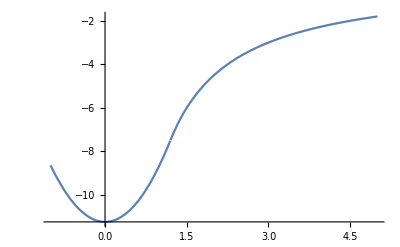

```mathematica
Plot[VC[x,10,1.2]/10^10,{x,-1,5}]
```